## Define the Gaussian radial basis.

```mathematica
g[r_]:=1/(σ √(2 π))Exp[-1/(2 σ^2)(r-(n rc)/(N-1))^2](1/2(Cos[(π r)/rc]+1))
```

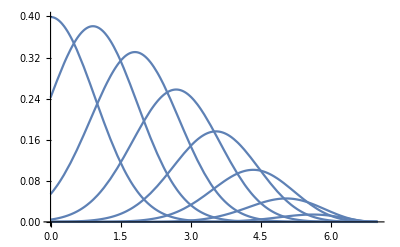

```mathematica
Plot[Table[g[r],{σ,{1}},{N,{8}},{n,{0,1,2,3,4,5, 6, 7}},{rc,{7}}],{r,0,7},PlotRange->{{0,7},{0,0.4}}]
```

## Calculate the gradient.

```mathematica
D[g[r],r]//FullSimplify
```

(ⅇ^(-(r-(n rc)/(-1+N))^2/(2 σ^2)) (rc (r-N r+n rc) (1+Cos[(π r)/rc])-(-1+N) π σ^2 Sin[(π r)/rc]))/(2 (-1+N) √(2 π) rc σ^3)

```mathematica
D[(1/2(Cos[(π r)/rc]+1)),r]//FullSimplify
```

-(π Sin[(π r)/rc])/(2 rc)

```mathematica
D[1/(σ √(2 π))Exp[-1/(2 σ^2)(r-(n rc)/(N-1))^2],r]//FullSimplify
```

-(ⅇ^(-(r-(n rc)/(-1+N))^2/(2 σ^2)) (r-(n rc)/(-1+N)))/(√(2 π) σ^3)